# L=2

```mathematica
l=2;
```

```mathematica
NoKernels=21;
```

## Setup

This function takes a value of lambda and returns the 100 eigenvalues of the hamiltonian which have the lowest absolute value. nn is the matrix size, dρ is the step size, and ρinf is numerical infinity for the problem.

Because the results of the calculation are highly sensitive to changes in ρinf, I pinned ρinf to λ.

```mathematica
RoughCritical[λ_]:=Module[{H,res,dρ,ρinf,nn},
dρ=0.1;
ρinf=Round[20*λ];
nn=Round[ρinf/dρ];
(*Print["dρ = "<>ToString[dρ]<>", ρinf = "<>ToString[ρinf]<>", and nn = "<>ToString[nn]<>"."];*)
H=SparseArray[{{n_,n_}->2./dρ^2-2./(n*dρ)ⅇ^(-n*dρ/λ)+(l*(l+1))/(n*dρ)^2,{n_, m_}/; Abs[n-m] == 1 -> -1./dρ^2},{nn,nn}, 0.];
res=Sort[Eigenvalues[H,-100]];(*Went from 100 down to 25 eigenvalues, which sped this calculation up immensely with no apparent loss of information*)
Return[res]
]
```

```mathematica
CountNegs[list_]:=Module[{neg,i},
neg=0;
For[i=1,list[[i]]<0,i++,
neg++;
];
Return[neg]
]
```

```mathematica
FindLs[l0_,lf_,val_,vaf_,range_]:=Module[{mid,vam,lnegs,mnegs,hnegs,res},
res={};
mid=l0+(lf-l0)/2;
lnegs=CountNegs[val];
vam=RoughCritical[mid];
mnegs=CountNegs[vam];
hnegs=CountNegs[vaf];
If[lf-l0>range,
If[lnegs<mnegs ||(lnegs==mnegs && val[[1]] < vam[[1]]&& mnegs>0),
res=Join[res,FindLs[l0,mid,val,vam,range]];
Return[res]
];
If[mnegs<hnegs || (hnegs==mnegs && vam[[1]] < vaf[[1]]&&hnegs>0),
res=Join[res,FindLs[mid,lf,vam,vaf,range]];
Return[res]
];
,
Print["Found one!"];
Return[{{l0,lf}}];
]
]
```

## Finding candidate ranges

```mathematica
RangeChunk[low_,high_]:=Module[{res,val,vaf,lnegs,hnegs},
res={};
val=RoughCritical[low];
lnegs=CountNegs[val];
vaf=RoughCritical[high];
hnegs=CountNegs[vaf];
If[lnegs<hnegs || (lnegs==hnegs && val[[1]] < vaf[[1]]&& hnegs>0),
res=FindLs[low,high,val,vaf,1];
];
Return[res]
]
```

```mathematica
chunks=Table[{(i-1)*(1000-0.5)/NoKernels+0.5,i*(1000-0.5)/NoKernels+0.5},{i,1,NoKernels}]
```

{{0.5,48.0952},{48.0952,95.6905},{95.6905,143.286},{143.286,190.881},{190.881,238.476},{238.476,286.071},{286.071,333.667},{333.667,381.262},{381.262,428.857},{428.857,476.452},{476.452,524.048},{524.048,571.643},{571.643,619.238},{619.238,666.833},{666.833,714.429},{714.429,762.024},{762.024,809.619},{809.619,857.214},{857.214,904.81},{904.81,952.405},{952.405,1000.}}

```mathematica
DistributeDefinitions[RangeChunk,CountNegs,chunks,FindLs,RoughCritical,l]
```

```mathematica
rangesrough=ParallelTable[RangeChunk[chunks[[i,1]],chunks[[i,2]]],{i,1,Length[chunks]}];
```

Found one!

Found one!

Found one!

«18 more identical outputs»

```mathematica
ranges={};
```

```mathematica
For[i=1,i<Length[rangesrough],i++,
ranges=Join[ranges,rangesrough[[i]]];
]
```

```mathematica
ranges
```

{{10.9115,11.6551},{57.0193,57.763},{103.871,104.615},{164.109,164.852},{212.448,213.191},{238.476,239.22},{295.739,296.483},{359.695,360.439},{393.904,394.648},{429.601,430.344},{506.199,506.943},{546.358,547.102},{588.747,589.491},{631.881,632.624},{677.245,677.988},{724.096,724.84},{772.435,773.179},{822.262,823.005},{873.575,874.319},{926.376,927.12}}

```mathematica
Length[ranges]
```

20

## Rootfinding for Lcs

### Setup

```mathematica
Critical[λ_,consts_]:=Module[{H,res,dρ,ρinf,nn},
dρ=consts[[1]];
ρinf=Round[consts[[2]]];
nn=Round[ρinf/dρ];
(*Print["dρ = "<>ToString[dρ]<>", ρinf = "<>ToString[ρinf]<>", and nn = "<>ToString[nn]<>"."];*)
H=SparseArray[{{n_,n_}->2./dρ^2-2./(n*dρ)ⅇ^(-n*dρ/λ)+(l(l+1))/(n*dρ)^2,{n_, m_}/; Abs[n-m] == 1 -> -1./dρ^2},{nn,nn}, 0.];
res=Sort[Eigenvalues[H,-25]];(*Went from 100 down to 25 eigenvalues, which sped this calculation up immensely with no apparent loss of information*)
Return[res]
]
```

```mathematica
Bisect[F_,consts_,x0_,xf_,ϵ_]:=Module[{mid,val,lnegs,vam,mnegs,vah},
mid=x0+Abs[x0-xf]/2;
Print["Bisecting. Midpoint is "<>ToString[mid]];
val=F[x0,consts];
lnegs=CountNegs[val];
vam=F[mid,consts];
mnegs=CountNegs[vam];
If[xf-x0>ϵ,
(*Print[{lnegs,mnegs},{val[[1]],vam[[1]]}];*)
If[lnegs<mnegs || (lnegs==mnegs && val[[1]] < vam[[1]]), (*if there is a zero on the lower half*)
Return[Bisect[F,consts,x0,mid,ϵ]];, (*bisect it*)
Return[Bisect[F,consts,mid,xf,ϵ]]; (*otherwise try the upper half*)
];,
vah = F[xf,consts];
Return[{mid,lnegs,CountNegs[vah]}];
]
]
```

```mathematica
Findlc[input_,i_,eps_]:=Module[{val,vah,lnegs,hnegs,res},
Print["***Beginning to calculate the "<>ToString[i]<>"th lambda, part "<>ToString[input[[1]]]];
val=Critical[input[[3]],{0.1,input[[2]],input[[2]]/0.1}];
vah=Critical[input[[4]],{0.1,input[[2]],input[[2]]/0.1}];
lnegs=CountNegs[val];
hnegs=CountNegs[vah];
If[lnegs<hnegs || (lnegs==hnegs && val[[1]]<vah[[1]]),(*doublechecks for zero*)
Print["Pass!"];
res={input[[1]],Bisect[Critical,{0.1,input[[2]],input[[2]]/0.1},input[[3]],input[[4]],eps]};
,(*else*)
Print["Fail!"];
res={input[[1]],Null};
];
Return[res]
]
```

```mathematica
ListRandomize[list_]:=Module[{order,res},
order=Table[{RandomReal[],i},{i,1,Length[list]}];
order = Sort[order];
res=Table[list[[order[[i,2]]]],{i,1,Length[list]}];
Return[res]
]
```

```mathematica
rhoinfs={40,80};
```

### First calculations: refinement

```mathematica
inputslow=Table[{i,rhoinfs[[1]]*ranges[[i,1]],ranges[[i,1]]-2,ranges[[i,2]]+2},{i,1,Length[ranges]}];
```

```mathematica
inputslow=ListRandomize[inputslow];
```

```mathematica
DistributeDefinitions[Critical,Bisect,CountNegs,Findlc,inputslow]
```

```mathematica
refinement=ParallelTable[Findlc[inputslow[[i]],i,0.25],{i,1,Length[inputslow]}]
```

***Beginning to calculate the 1th lambda, part 5

***Beginning to calculate the 2th lambda, part 14

***Beginning to calculate the 3th lambda, part 6

***Beginning to calculate the 4th lambda, part 2

***Beginning to calculate the 5th lambda, part 10

***Beginning to calculate the 6th lambda, part 11

***Beginning to calculate the 7th lambda, part 16

***Beginning to calculate the 8th lambda, part 19

***Beginning to calculate the 9th lambda, part 4

***Beginning to calculate the 10th lambda, part 1

***Beginning to calculate the 11th lambda, part 3

***Beginning to calculate the 12th lambda, part 13

***Beginning to calculate the 13th lambda, part 7

***Beginning to calculate the 14th lambda, part 18

***Beginning to calculate the 15th lambda, part 8

***Beginning to calculate the 16th lambda, part 20

***Beginning to calculate the 17th lambda, part 9

***Beginning to calculate the 18th lambda, part 12

***Beginning to calculate the 19th lambda, part 17

***Beginning to calculate the 20th lambda, part 15

Pass!

Pass!

Bisecting. Midpoint is 57.3912

Bisecting. Midpoint is 11.2833

Bisecting. Midpoint is 10.0974

Bisecting. Midpoint is 10.6903

Bisecting. Midpoint is 10.9868

Bisecting. Midpoint is 10.8386

Bisecting. Midpoint is 10.9127

Bisecting. Midpoint is 58.5771

Pass!

Bisecting. Midpoint is 104.243

Bisecting. Midpoint is 57.9841

Bisecting. Midpoint is 57.6877

Pass!

Bisecting. Midpoint is 164.48

Pass!

Bisecting. Midpoint is 212.819

Bisecting. Midpoint is 57.5394

Pass!

Bisecting. Midpoint is 238.848

Bisecting. Midpoint is 57.4653

Bisecting. Midpoint is 103.057

Pass!

Bisecting. Midpoint is 429.973

Pass!

Bisecting. Midpoint is 163.295

Bisecting. Midpoint is 506.571

Bisecting. Midpoint is 211.633

Pass!

Bisecting. Midpoint is 296.111

Bisecting. Midpoint is 240.034

Bisecting. Midpoint is 103.65

Pass!

Bisecting. Midpoint is 632.252

Pass!

Bisecting. Midpoint is 360.067

Bisecting. Midpoint is 103.946

Bisecting. Midpoint is 212.226

Pass!

Bisecting. Midpoint is 394.276

Pass!

Bisecting. Midpoint is 724.468

Bisecting. Midpoint is 163.888

Bisecting. Midpoint is 239.441

Bisecting. Midpoint is 103.798

Bisecting. Midpoint is 431.159

Bisecting. Midpoint is 212.523

Pass!

Bisecting. Midpoint is 873.947

Bisecting. Midpoint is 164.184

Bisecting. Midpoint is 239.145

Bisecting. Midpoint is 505.385

Pass!

Bisecting. Midpoint is 546.73

Bisecting. Midpoint is 103.872

Pass!

Bisecting. Midpoint is 589.119

Bisecting. Midpoint is 297.297

Bisecting. Midpoint is 212.375

Bisecting. Midpoint is 633.438

Bisecting. Midpoint is 164.332

Bisecting. Midpoint is 238.996

Pass!

Bisecting. Midpoint is 677.617

Bisecting. Midpoint is 430.566

Bisecting. Midpoint is 212.449

Pass!

Bisecting. Midpoint is 822.633

Bisecting. Midpoint is 164.406

Bisecting. Midpoint is 358.881

Bisecting. Midpoint is 393.09

Bisecting. Midpoint is 723.282

Pass!

Bisecting. Midpoint is 772.807

Bisecting. Midpoint is 238.922

Bisecting. Midpoint is 505.978

Bisecting. Midpoint is 632.845

Bisecting. Midpoint is 430.269

Pass!

Bisecting. Midpoint is 926.748

Bisecting. Midpoint is 296.704

Bisecting. Midpoint is 875.133

Bisecting. Midpoint is 587.933

Bisecting. Midpoint is 506.275

Bisecting. Midpoint is 547.916

Bisecting. Midpoint is 359.474

Bisecting. Midpoint is 393.683

Bisecting. Midpoint is 723.875

Bisecting. Midpoint is 632.549

Bisecting. Midpoint is 430.121

Bisecting. Midpoint is 296.408

Bisecting. Midpoint is 676.431

Bisecting. Midpoint is 506.423

Bisecting. Midpoint is 430.047

Bisecting. Midpoint is 632.401

Bisecting. Midpoint is 874.54

Bisecting. Midpoint is 359.771

Bisecting. Midpoint is 588.526

Bisecting. Midpoint is 393.98

Bisecting. Midpoint is 821.447

Bisecting. Midpoint is 771.621

Bisecting. Midpoint is 724.172

Bisecting. Midpoint is 296.259

Bisecting. Midpoint is 506.349

Bisecting. Midpoint is 547.323

Bisecting. Midpoint is 632.475

Bisecting. Midpoint is 359.919

Bisecting. Midpoint is 296.333

Bisecting. Midpoint is 927.934

Bisecting. Midpoint is 588.823

Bisecting. Midpoint is 874.243

Bisecting. Midpoint is 394.128

Bisecting. Midpoint is 724.32

Bisecting. Midpoint is 677.024

Bisecting. Midpoint is 359.993

Bisecting. Midpoint is 547.026

Bisecting. Midpoint is 724.394

Bisecting. Midpoint is 394.202

Bisecting. Midpoint is 874.095

Bisecting. Midpoint is 588.675

Bisecting. Midpoint is 772.214

Bisecting. Midpoint is 822.04

Bisecting. Midpoint is 874.021

Bisecting. Midpoint is 677.32

Bisecting. Midpoint is 588.749

Bisecting. Midpoint is 546.878

Bisecting. Midpoint is 927.341

Bisecting. Midpoint is 772.511

Bisecting. Midpoint is 546.804

Bisecting. Midpoint is 822.337

Bisecting. Midpoint is 677.468

Bisecting. Midpoint is 927.044

Bisecting. Midpoint is 772.659

Bisecting. Midpoint is 677.543

Bisecting. Midpoint is 822.485

Bisecting. Midpoint is 772.585

Bisecting. Midpoint is 926.896

Bisecting. Midpoint is 822.559

Bisecting. Midpoint is 926.97

{{5,{212.449,1,2}},{14,{632.475,1,2}},{6,{238.922,1,2}},{2,{57.4653,1,2}},{10,{430.047,1,2}},{11,{506.349,1,2}},{16,{724.394,1,2}},{19,{874.021,1,2}},{4,{164.406,1,2}},{1,{10.9127,0,1}},{3,{103.872,1,2}},{13,{588.749,1,2}},{7,{296.333,1,2}},{18,{822.559,1,2}},{8,{359.993,1,2}},{20,{926.97,1,2}},{9,{394.202,1,2}},{12,{546.804,1,2}},{17,{772.585,1,2}},{15,{677.543,1,2}}}

```mathematica
refinement=Sort[refinement];
```

```mathematica
inputshigh=Table[{i,rhoinfs[[1]]*refinement[[i,2,1]],refinement[[i,2,1]]-0.75,refinement[[i,2,1]]+0.75},{i,1,Length[refinement]}];
```

```mathematica
inputshigh=ListRandomize[inputshigh]
```

{{11,20254.,505.599,507.099},{17,30903.4,771.835,773.335},{9,15768.1,393.452,394.952},{8,14399.7,359.243,360.743},{13,23549.9,587.999,589.499},{6,9556.89,238.172,239.672},{5,8497.95,211.699,213.199},{14,25299.,631.725,633.225},{12,21872.2,546.054,547.554},{3,4154.89,103.122,104.622},{18,32902.4,821.809,823.309},{19,34960.8,873.271,874.771},{2,2298.61,56.7153,58.2153},{15,27101.7,676.793,678.293},{7,11853.3,295.583,297.083},{1,436.508,10.1627,11.6627},{4,6576.25,163.656,165.156},{16,28975.8,723.644,725.144},{10,17201.9,429.297,430.797},{20,37078.8,926.22,927.72}}

```mathematica
Length[inputshigh]
```

20

```mathematica
DistributeDefinitions[inputshigh]
```

```mathematica
refinement2=ParallelTable[Findlc[inputshigh[[i]],i,1/32.],{i,1,Length[inputshigh]}]
```

***Beginning to calculate the 1th lambda, part 11

***Beginning to calculate the 2th lambda, part 17

***Beginning to calculate the 3th lambda, part 9

***Beginning to calculate the 4th lambda, part 8

***Beginning to calculate the 5th lambda, part 13

***Beginning to calculate the 6th lambda, part 6

***Beginning to calculate the 7th lambda, part 5

***Beginning to calculate the 8th lambda, part 14

***Beginning to calculate the 9th lambda, part 12

***Beginning to calculate the 10th lambda, part 3

***Beginning to calculate the 11th lambda, part 18

***Beginning to calculate the 12th lambda, part 19

***Beginning to calculate the 13th lambda, part 2

***Beginning to calculate the 14th lambda, part 15

***Beginning to calculate the 15th lambda, part 7

***Beginning to calculate the 16th lambda, part 1

***Beginning to calculate the 17th lambda, part 4

***Beginning to calculate the 18th lambda, part 16

***Beginning to calculate the 19th lambda, part 10

***Beginning to calculate the 20th lambda, part 20

Pass!

Bisecting. Midpoint is 10.9127

Bisecting. Midpoint is 11.2877

Bisecting. Midpoint is 11.1002

Bisecting. Midpoint is 11.0064

Pass!

Bisecting. Midpoint is 10.9596

Bisecting. Midpoint is 57.4653

Bisecting. Midpoint is 10.9361

Bisecting. Midpoint is 10.9479

Bisecting. Midpoint is 57.8403

Pass!

Bisecting. Midpoint is 103.872

Pass!

Bisecting. Midpoint is 212.449

Pass!

Bisecting. Midpoint is 238.922

Bisecting. Midpoint is 57.6528

Pass!

Bisecting. Midpoint is 164.406

Bisecting. Midpoint is 57.5591

Bisecting. Midpoint is 104.247

Pass!

Bisecting. Midpoint is 359.993

Bisecting. Midpoint is 57.5122

Bisecting. Midpoint is 212.824

Bisecting. Midpoint is 57.4887

Bisecting. Midpoint is 238.547

Pass!

Bisecting. Midpoint is 394.202

Pass!

Bisecting. Midpoint is 296.333

Bisecting. Midpoint is 104.06

Bisecting. Midpoint is 57.5005

Bisecting. Midpoint is 164.031

Pass!

Bisecting. Midpoint is 588.749

Pass!

Bisecting. Midpoint is 506.349

Bisecting. Midpoint is 212.636

Pass!

Bisecting. Midpoint is 632.475

Pass!

Bisecting. Midpoint is 772.585

Bisecting. Midpoint is 238.735

Bisecting. Midpoint is 360.368

Bisecting. Midpoint is 103.966

Pass!

Bisecting. Midpoint is 430.047

Bisecting. Midpoint is 212.543

Bisecting. Midpoint is 295.958

Bisecting. Midpoint is 164.219

Bisecting. Midpoint is 394.577

Bisecting. Midpoint is 103.919

Bisecting. Midpoint is 238.828

Pass!

Bisecting. Midpoint is 546.804

Bisecting. Midpoint is 212.496

Pass!

Bisecting. Midpoint is 677.543

Bisecting. Midpoint is 103.942

Bisecting. Midpoint is 164.313

Bisecting. Midpoint is 360.181

Bisecting. Midpoint is 589.124

Bisecting. Midpoint is 238.875

Bisecting. Midpoint is 505.974

Bisecting. Midpoint is 103.931

Bisecting. Midpoint is 296.146

Bisecting. Midpoint is 632.1

Bisecting. Midpoint is 212.472

Pass!

Bisecting. Midpoint is 724.394

Bisecting. Midpoint is 394.39

Bisecting. Midpoint is 238.852

Bisecting. Midpoint is 164.359

Bisecting. Midpoint is 212.461

Pass!

Bisecting. Midpoint is 822.559

Bisecting. Midpoint is 429.672

Bisecting. Midpoint is 360.087

Bisecting. Midpoint is 296.24

Bisecting. Midpoint is 238.864

Bisecting. Midpoint is 772.96

Pass!

Bisecting. Midpoint is 874.021

Bisecting. Midpoint is 164.383

Bisecting. Midpoint is 506.161

Bisecting. Midpoint is 588.936

Pass!

Bisecting. Midpoint is 926.97

Bisecting. Midpoint is 394.296

Bisecting. Midpoint is 632.287

Bisecting. Midpoint is 677.918

Bisecting. Midpoint is 546.429

Bisecting. Midpoint is 296.287

Bisecting. Midpoint is 164.371

Bisecting. Midpoint is 360.04

Bisecting. Midpoint is 506.255

Bisecting. Midpoint is 296.31

Bisecting. Midpoint is 429.859

Bisecting. Midpoint is 394.249

Bisecting. Midpoint is 588.842

Bisecting. Midpoint is 360.063

Bisecting. Midpoint is 772.772

Bisecting. Midpoint is 724.019

Bisecting. Midpoint is 822.184

Bisecting. Midpoint is 632.381

Bisecting. Midpoint is 296.322

Bisecting. Midpoint is 394.272

Bisecting. Midpoint is 677.73

Bisecting. Midpoint is 360.052

Bisecting. Midpoint is 546.616

Bisecting. Midpoint is 506.302

Bisecting. Midpoint is 429.953

Bisecting. Midpoint is 588.796

Bisecting. Midpoint is 873.646

Bisecting. Midpoint is 394.261

Bisecting. Midpoint is 632.428

Bisecting. Midpoint is 927.345

Bisecting. Midpoint is 772.678

Bisecting. Midpoint is 506.279

Bisecting. Midpoint is 430.

Bisecting. Midpoint is 677.636

Bisecting. Midpoint is 724.207

Bisecting. Midpoint is 822.372

Bisecting. Midpoint is 588.819

Bisecting. Midpoint is 546.71

Bisecting. Midpoint is 632.404

Bisecting. Midpoint is 506.29

Bisecting. Midpoint is 430.023

Bisecting. Midpoint is 588.807

Bisecting. Midpoint is 772.632

Bisecting. Midpoint is 677.589

Bisecting. Midpoint is 632.416

Bisecting. Midpoint is 873.834

Bisecting. Midpoint is 546.757

Bisecting. Midpoint is 822.466

Bisecting. Midpoint is 724.3

Bisecting. Midpoint is 430.035

Bisecting. Midpoint is 772.655

Bisecting. Midpoint is 927.158

Bisecting. Midpoint is 677.566

Bisecting. Midpoint is 772.643

Bisecting. Midpoint is 546.78

Bisecting. Midpoint is 822.512

Bisecting. Midpoint is 677.578

Bisecting. Midpoint is 873.927

Bisecting. Midpoint is 724.347

Bisecting. Midpoint is 546.769

Bisecting. Midpoint is 927.064

Bisecting. Midpoint is 822.536

Bisecting. Midpoint is 724.324

Bisecting. Midpoint is 873.974

Bisecting. Midpoint is 927.017

Bisecting. Midpoint is 724.335

Bisecting. Midpoint is 822.524

Bisecting. Midpoint is 873.951

Bisecting. Midpoint is 926.994

Bisecting. Midpoint is 873.963

Bisecting. Midpoint is 926.982

{{11,{506.29,1,2}},{17,{772.643,1,2}},{9,{394.261,1,2}},{8,{360.052,1,2}},{13,{588.807,1,2}},{6,{238.864,1,2}},{5,{212.461,1,2}},{14,{632.416,1,2}},{12,{546.769,1,2}},{3,{103.931,1,2}},{18,{822.524,1,2}},{19,{873.963,1,2}},{2,{57.5005,1,2}},{15,{677.578,1,2}},{7,{296.322,1,2}},{1,{10.9479,0,1}},{4,{164.371,1,2}},{16,{724.335,1,2}},{10,{430.035,1,2}},{20,{926.982,1,2}}}

```mathematica
refinement2=Sort[refinement2];
```

### Second calculation: lcs for real

```mathematica
ref1ins= Table[{i,rhoinfs[[1]]*refinement[[i,2,1]],refinement[[i,2,1]]-1/4.,refinement[[i,2,1]]+1/4.},{i,1,Length[refinement]}];
```

```mathematica
ref2ins=Table[{i+Length[ref1ins],rhoinfs[[2]]*refinement2[[i,2,1]],refinement2[[i,2,1]]-1/64.,refinement2[[i,2,1]]+1/64.},{i,1,Length[refinement2]}];
```

```mathematica
newins=Join[Sort[ref1ins],Sort[ref2ins]];
```

```mathematica
newins=ListRandomize[newins]
```

{{34,50593.3,632.401,632.432},{30,34402.8,430.019,430.051},{23,8314.46,103.915,103.946},{35,54206.2,677.562,677.593},{24,13149.7,164.356,164.387},{13,23549.9,588.499,588.999},{12,21872.2,546.554,547.054},{27,23705.7,296.306,296.337},{18,32902.4,822.309,822.809},{9,15768.1,393.952,394.452},{20,37078.8,926.72,927.22},{8,14399.7,359.743,360.243},{2,2298.61,57.2153,57.7153},{21,875.828,10.9322,10.9635},{22,4600.04,57.4848,57.5161},{39,69917.,873.947,873.978},{38,65801.9,822.508,822.54},{33,47104.6,588.792,588.823},{7,11853.3,296.083,296.583},{26,19109.1,238.848,238.879},{16,28975.8,724.144,724.644},{37,61811.5,772.628,772.659},{19,34960.8,873.771,874.271},{10,17201.9,429.797,430.297},{1,436.508,10.6627,11.1627},{5,8497.95,212.199,212.699},{32,43741.5,546.753,546.784},{14,25299.,632.225,632.725},{17,30903.4,772.335,772.835},{28,28804.1,360.036,360.067},{40,74158.6,926.966,926.998},{6,9556.89,238.672,239.172},{31,40503.2,506.275,506.306},{25,16996.8,212.445,212.476},{4,6576.25,164.156,164.656},{3,4154.89,103.622,104.122},{36,57946.8,724.32,724.351},{29,31540.9,394.245,394.276},{15,27101.7,677.293,677.793},{11,20254.,506.099,506.599}}

```mathematica
Length[newins]
```

40

```mathematica
DistributeDefinitions[newins]
```

```mathematica
lcs=ParallelTable[Findlc[newins[[i]],i,10^-6],{i,1,Length[newins]}]
```

***Beginning to calculate the 1th lambda, part 34

***Beginning to calculate the 3th lambda, part 23

***Beginning to calculate the 5th lambda, part 24

***Beginning to calculate the 7th lambda, part 12

***Beginning to calculate the 9th lambda, part 18

***Beginning to calculate the 11th lambda, part 20

***Beginning to calculate the 13th lambda, part 2

***Beginning to calculate the 15th lambda, part 22

***Beginning to calculate the 17th lambda, part 38

***Beginning to calculate the 19th lambda, part 7

***Beginning to calculate the 21th lambda, part 16

***Beginning to calculate the 23th lambda, part 19

***Beginning to calculate the 25th lambda, part 1

***Beginning to calculate the 27th lambda, part 32

***Beginning to calculate the 29th lambda, part 17

***Beginning to calculate the 31th lambda, part 40

***Beginning to calculate the 33th lambda, part 31

***Beginning to calculate the 35th lambda, part 4

***Beginning to calculate the 37th lambda, part 36

***Beginning to calculate the 39th lambda, part 15

***Beginning to calculate the 40th lambda, part 11

Pass!

Pass!

Pass!

Bisecting. Midpoint is 57.4653

Bisecting. Midpoint is 57.5005

Bisecting. Midpoint is 10.9127

Bisecting. Midpoint is 57.5903

Bisecting. Midpoint is 11.0377

Bisecting. Midpoint is 57.5278

Bisecting. Midpoint is 10.9752

Bisecting. Midpoint is 10.9439

Bisecting. Midpoint is 10.9596

Bisecting. Midpoint is 10.9518

Bisecting. Midpoint is 10.9479

Bisecting. Midpoint is 10.9459

Bisecting. Midpoint is 10.9469

Bisecting. Midpoint is 10.9474

Bisecting. Midpoint is 10.9476

Bisecting. Midpoint is 10.9475

Bisecting. Midpoint is 57.4966

Bisecting. Midpoint is 57.5083

Bisecting. Midpoint is 10.9474

Bisecting. Midpoint is 10.9474

Bisecting. Midpoint is 10.9474

«1 more identical outputs»

Pass!

Bisecting. Midpoint is 10.9474

Bisecting. Midpoint is 103.931

Bisecting. Midpoint is 10.9474

Pass!

Bisecting. Midpoint is 10.9474

Bisecting. Midpoint is 164.406

Bisecting. Midpoint is 57.5122

Bisecting. Midpoint is 10.9474

***Beginning to calculate the 26th lambda, part 5

Bisecting. Midpoint is 57.5044

Bisecting. Midpoint is 57.5044

Bisecting. Midpoint is 57.5005

Pass!

Bisecting. Midpoint is 164.371

Bisecting. Midpoint is 57.5024

Bisecting. Midpoint is 57.5024

Bisecting. Midpoint is 103.939

Bisecting. Midpoint is 57.5014

Pass!

Bisecting. Midpoint is 296.333

Bisecting. Midpoint is 57.5014

Bisecting. Midpoint is 57.5009

Bisecting. Midpoint is 164.281

Bisecting. Midpoint is 57.5007

Pass!

Bisecting. Midpoint is 212.449

Bisecting. Midpoint is 57.5006

Bisecting. Midpoint is 57.5009

Pass!

Bisecting. Midpoint is 546.804

Bisecting. Midpoint is 57.5006

Bisecting. Midpoint is 103.935

Bisecting. Midpoint is 57.5007

Bisecting. Midpoint is 57.5007

Pass!

Bisecting. Midpoint is 822.559

Bisecting. Midpoint is 57.5007

Bisecting. Midpoint is 164.344

Bisecting. Midpoint is 57.5007

Bisecting. Midpoint is 57.5006

Bisecting. Midpoint is 164.379

Pass!

Bisecting. Midpoint is 926.97

Bisecting. Midpoint is 103.937

Bisecting. Midpoint is 57.5007

Bisecting. Midpoint is 57.5007

Bisecting. Midpoint is 212.574

Bisecting. Midpoint is 57.5006

Bisecting. Midpoint is 57.5007

Pass!

Bisecting. Midpoint is 506.349

Bisecting. Midpoint is 57.5007

Bisecting. Midpoint is 296.208

***Beginning to calculate the 14th lambda, part 21

Bisecting. Midpoint is 164.375

Bisecting. Midpoint is 103.938

Pass!

Bisecting. Midpoint is 57.5006

Bisecting. Midpoint is 10.9479

Bisecting. Midpoint is 10.94

Bisecting. Midpoint is 10.9439

Bisecting. Midpoint is 10.9459

Bisecting. Midpoint is 10.9469

Pass!

Bisecting. Midpoint is 677.543

Bisecting. Midpoint is 10.9474

Bisecting. Midpoint is 57.5006

Bisecting. Midpoint is 10.9476

Bisecting. Midpoint is 10.9475

Bisecting. Midpoint is 10.9474

Bisecting. Midpoint is 10.9474

Pass!

Bisecting. Midpoint is 724.394

Bisecting. Midpoint is 212.511

Bisecting. Midpoint is 10.9474

Bisecting. Midpoint is 164.375

Bisecting. Midpoint is 10.9474

Bisecting. Midpoint is 57.5006

Bisecting. Midpoint is 103.937

Bisecting. Midpoint is 10.9474

Bisecting. Midpoint is 10.9474

Bisecting. Midpoint is 10.9474

Bisecting. Midpoint is 546.679

Bisecting. Midpoint is 10.9474

Bisecting. Midpoint is 164.359

Bisecting. Midpoint is 57.5006

Pass!

Bisecting. Midpoint is 772.585

Pass!

Bisecting. Midpoint is 632.416

Bisecting. Midpoint is 57.5006

Bisecting. Midpoint is 103.937

Pass!

Bisecting. Midpoint is 874.021

Bisecting. Midpoint is 822.434

Bisecting. Midpoint is 57.5006

Bisecting. Midpoint is 212.48

Bisecting. Midpoint is 296.271

Bisecting. Midpoint is 927.095

Bisecting. Midpoint is 164.367

Bisecting. Midpoint is 57.5006

Bisecting. Midpoint is 164.373

Bisecting. Midpoint is 103.937

Pass!

Bisecting. Midpoint is 506.29

Pass!

Bisecting. Midpoint is 546.769

***Beginning to calculate the 16th lambda, part 39

Bisecting. Midpoint is 546.741

Bisecting. Midpoint is 164.371

Bisecting. Midpoint is 103.937

Bisecting. Midpoint is 212.464

Bisecting. Midpoint is 506.224

Bisecting. Midpoint is 296.302

Bisecting. Midpoint is 103.937

Bisecting. Midpoint is 164.374

Bisecting. Midpoint is 164.373

Bisecting. Midpoint is 822.497

Bisecting. Midpoint is 677.668

Bisecting. Midpoint is 212.472

Bisecting. Midpoint is 103.937

Bisecting. Midpoint is 927.033

Bisecting. Midpoint is 724.269

Bisecting. Midpoint is 546.773

Bisecting. Midpoint is 164.374

Pass!

Bisecting. Midpoint is 724.335

Bisecting. Midpoint is 103.937

Bisecting. Midpoint is 164.375

Bisecting. Midpoint is 296.318

Bisecting. Midpoint is 164.375

Bisecting. Midpoint is 772.71

Bisecting. Midpoint is 212.468

Bisecting. Midpoint is 103.937

Pass!

Bisecting. Midpoint is 822.524

Bisecting. Midpoint is 546.757

Bisecting. Midpoint is 164.375

Bisecting. Midpoint is 103.937

Bisecting. Midpoint is 822.528

Bisecting. Midpoint is 873.896

Bisecting. Midpoint is 212.466

Bisecting. Midpoint is 164.375

Bisecting. Midpoint is 927.002

Bisecting. Midpoint is 296.326

Bisecting. Midpoint is 506.286

Bisecting. Midpoint is 103.937

Bisecting. Midpoint is 632.408

Bisecting. Midpoint is 164.375

Pass!

Bisecting. Midpoint is 926.982

Bisecting. Midpoint is 212.467

Bisecting. Midpoint is 103.937

Pass!

Bisecting. Midpoint is 873.963

Bisecting. Midpoint is 677.605

Bisecting. Midpoint is 506.282

Bisecting. Midpoint is 546.765

Bisecting. Midpoint is 164.375

Bisecting. Midpoint is 164.375

Bisecting. Midpoint is 546.761

Bisecting. Midpoint is 296.322

Bisecting. Midpoint is 724.332

Bisecting. Midpoint is 212.468

***Beginning to calculate the 4th lambda, part 35

Bisecting. Midpoint is 822.512

Bisecting. Midpoint is 164.375

Bisecting. Midpoint is 926.986

Bisecting. Midpoint is 164.375

Bisecting. Midpoint is 772.647

Bisecting. Midpoint is 212.468

Bisecting. Midpoint is 546.761

Bisecting. Midpoint is 164.375

Bisecting. Midpoint is 296.324

Bisecting. Midpoint is 506.318

Bisecting. Midpoint is 164.375

Bisecting. Midpoint is 164.375

Bisecting. Midpoint is 212.467

Bisecting. Midpoint is 822.52

Bisecting. Midpoint is 873.959

Bisecting. Midpoint is 164.375

Bisecting. Midpoint is 926.978

Bisecting. Midpoint is 677.574

Bisecting. Midpoint is 546.763

Bisecting. Midpoint is 296.325

Bisecting. Midpoint is 164.375

Bisecting. Midpoint is 212.468

Bisecting. Midpoint is 724.3

Bisecting. Midpoint is 632.404

Bisecting. Midpoint is 164.375

Bisecting. Midpoint is 164.375

Bisecting. Midpoint is 873.955

Bisecting. Midpoint is 724.328

Bisecting. Midpoint is 212.467

Bisecting. Midpoint is 546.762

Bisecting. Midpoint is 164.375

Bisecting. Midpoint is 164.375

Bisecting. Midpoint is 506.302

Bisecting. Midpoint is 822.516

Bisecting. Midpoint is 506.286

Bisecting. Midpoint is 296.325

Bisecting. Midpoint is 926.974

Bisecting. Midpoint is 772.616

Bisecting. Midpoint is 212.468

Bisecting. Midpoint is 164.375

Pass!

Bisecting. Midpoint is 677.578

Bisecting. Midpoint is 164.375

Bisecting. Midpoint is 546.757

Bisecting. Midpoint is 546.761

Bisecting. Midpoint is 822.516

Bisecting. Midpoint is 677.589

Bisecting. Midpoint is 212.467

Bisecting. Midpoint is 296.325

***Beginning to calculate the 36th lambda, part 3

Bisecting. Midpoint is 164.375

Bisecting. Midpoint is 822.514

Pass!

Bisecting. Midpoint is 103.872

Bisecting. Midpoint is 873.99

Bisecting. Midpoint is 926.972

Bisecting. Midpoint is 724.316

Bisecting. Midpoint is 212.468

Bisecting. Midpoint is 506.294

Bisecting. Midpoint is 103.997

Bisecting. Midpoint is 164.375

Bisecting. Midpoint is 103.935

Bisecting. Midpoint is 546.761

Bisecting. Midpoint is 296.325

Bisecting. Midpoint is 632.406

Bisecting. Midpoint is 212.468

Bisecting. Midpoint is 103.966

Bisecting. Midpoint is 873.959

Bisecting. Midpoint is 822.515

Bisecting. Midpoint is 103.95

Bisecting. Midpoint is 212.468

Bisecting. Midpoint is 772.632

Bisecting. Midpoint is 926.973

Bisecting. Midpoint is 926.974

Bisecting. Midpoint is 103.942

Bisecting. Midpoint is 296.325

Bisecting. Midpoint is 677.582

***Beginning to calculate the 6th lambda, part 13

Bisecting. Midpoint is 677.585

Bisecting. Midpoint is 212.468

Bisecting. Midpoint is 546.761

Bisecting. Midpoint is 506.284

Bisecting. Midpoint is 103.939

Bisecting. Midpoint is 506.29

Bisecting. Midpoint is 103.937

Bisecting. Midpoint is 103.938

Bisecting. Midpoint is 724.324

Bisecting. Midpoint is 296.325

Bisecting. Midpoint is 822.515

Bisecting. Midpoint is 873.974

Bisecting. Midpoint is 926.974

Bisecting. Midpoint is 103.937

Bisecting. Midpoint is 724.324

Bisecting. Midpoint is 546.761

Pass!

Bisecting. Midpoint is 588.749

Bisecting. Midpoint is 103.937

Bisecting. Midpoint is 546.759

Bisecting. Midpoint is 296.325

Bisecting. Midpoint is 103.937

Bisecting. Midpoint is 632.407

Bisecting. Midpoint is 772.639

Bisecting. Midpoint is 677.585

Bisecting. Midpoint is 103.937

Bisecting. Midpoint is 506.288

Bisecting. Midpoint is 822.515

Bisecting. Midpoint is 873.957

Bisecting. Midpoint is 546.761

Bisecting. Midpoint is 103.937

Bisecting. Midpoint is 926.973

Bisecting. Midpoint is 588.874

Bisecting. Midpoint is 296.325

Bisecting. Midpoint is 103.937

Bisecting. Midpoint is 677.582

Bisecting. Midpoint is 103.937

Bisecting. Midpoint is 822.512

Bisecting. Midpoint is 724.328

Bisecting. Midpoint is 103.937

Bisecting. Midpoint is 546.761

Bisecting. Midpoint is 296.325

Bisecting. Midpoint is 506.285

Bisecting. Midpoint is 822.515

Bisecting. Midpoint is 772.636

Bisecting. Midpoint is 103.937

Bisecting. Midpoint is 873.966

Bisecting. Midpoint is 926.973

Bisecting. Midpoint is 588.811

Bisecting. Midpoint is 103.937

Bisecting. Midpoint is 506.287

Bisecting. Midpoint is 677.584

Bisecting. Midpoint is 103.937

Bisecting. Midpoint is 296.325

Bisecting. Midpoint is 632.408

Bisecting. Midpoint is 546.761

Bisecting. Midpoint is 822.515

Bisecting. Midpoint is 546.76

Bisecting. Midpoint is 926.973

Bisecting. Midpoint is 588.78

Bisecting. Midpoint is 296.325

Bisecting. Midpoint is 873.958

Bisecting. Midpoint is 724.326

Bisecting. Midpoint is 772.637

Bisecting. Midpoint is 724.326

Bisecting. Midpoint is 926.97

Bisecting. Midpoint is 546.761

Bisecting. Midpoint is 506.287

Bisecting. Midpoint is 677.585

Bisecting. Midpoint is 296.325

Bisecting. Midpoint is 677.584

Bisecting. Midpoint is 822.515

Bisecting. Midpoint is 506.285

Bisecting. Midpoint is 926.973

Bisecting. Midpoint is 873.963

Bisecting. Midpoint is 588.796

Bisecting. Midpoint is 546.761

Bisecting. Midpoint is 632.408

***Beginning to calculate the 20th lambda, part 26

Bisecting. Midpoint is 822.515

Bisecting. Midpoint is 506.287

Bisecting. Midpoint is 546.761

Bisecting. Midpoint is 926.973

Bisecting. Midpoint is 546.759

Bisecting. Midpoint is 588.803

Bisecting. Midpoint is 724.327

Bisecting. Midpoint is 772.637

Bisecting. Midpoint is 677.585

Bisecting. Midpoint is 873.957

Bisecting. Midpoint is 506.285

Bisecting. Midpoint is 546.761

Bisecting. Midpoint is 822.51

Pass!

Bisecting. Midpoint is 238.864

Bisecting. Midpoint is 822.515

Bisecting. Midpoint is 588.799

Bisecting. Midpoint is 926.973

Bisecting. Midpoint is 677.583

Bisecting. Midpoint is 873.961

Bisecting. Midpoint is 506.287

Bisecting. Midpoint is 632.408

Bisecting. Midpoint is 588.801

Bisecting. Midpoint is 724.325

Bisecting. Midpoint is 724.327

Bisecting. Midpoint is 822.515

Bisecting. Midpoint is 772.637

Bisecting. Midpoint is 677.585

Bisecting. Midpoint is 238.856

***Beginning to calculate the 8th lambda, part 27

Bisecting. Midpoint is 926.973

Bisecting. Midpoint is 546.76

Bisecting. Midpoint is 873.957

Bisecting. Midpoint is 506.287

Bisecting. Midpoint is 588.802

Bisecting. Midpoint is 822.515

Bisecting. Midpoint is 506.285

Bisecting. Midpoint is 926.972

Pass!

Bisecting. Midpoint is 296.322

Bisecting. Midpoint is 926.973

Bisecting. Midpoint is 677.583

Bisecting. Midpoint is 238.86

Bisecting. Midpoint is 632.408

Bisecting. Midpoint is 724.327

Bisecting. Midpoint is 873.96

Bisecting. Midpoint is 677.585

Bisecting. Midpoint is 822.515

Bisecting. Midpoint is 588.802

Bisecting. Midpoint is 506.287

Bisecting. Midpoint is 926.973

Bisecting. Midpoint is 296.33

Bisecting. Midpoint is 772.637

Bisecting. Midpoint is 724.325

Bisecting. Midpoint is 238.858

Bisecting. Midpoint is 588.802

Bisecting. Midpoint is 873.958

Bisecting. Midpoint is 822.515

Bisecting. Midpoint is 677.585

Bisecting. Midpoint is 822.511

Bisecting. Midpoint is 724.328

Bisecting. Midpoint is 296.326

Bisecting. Midpoint is 926.973

Bisecting. Midpoint is 506.285

Bisecting. Midpoint is 632.408

Bisecting. Midpoint is 506.287

Bisecting. Midpoint is 546.76

Bisecting. Midpoint is 677.583

Bisecting. Midpoint is 873.96

Bisecting. Midpoint is 238.857

Bisecting. Midpoint is 772.637

Bisecting. Midpoint is 588.802

Bisecting. Midpoint is 296.324

***Beginning to calculate the 10th lambda, part 9

Bisecting. Midpoint is 588.802

Bisecting. Midpoint is 677.585

***Beginning to calculate the 12th lambda, part 8

Bisecting. Midpoint is 506.287

Bisecting. Midpoint is 238.856

Bisecting. Midpoint is 296.325

Pass!

Bisecting. Midpoint is 394.202

Bisecting. Midpoint is 724.328

Bisecting. Midpoint is 873.957

Bisecting. Midpoint is 772.637

Pass!

Bisecting. Midpoint is 359.993

Bisecting. Midpoint is 588.802

Bisecting. Midpoint is 926.971

Bisecting. Midpoint is 632.408

Bisecting. Midpoint is 394.327

Bisecting. Midpoint is 724.325

Bisecting. Midpoint is 360.118

Bisecting. Midpoint is 677.583

Bisecting. Midpoint is 873.96

Bisecting. Midpoint is 546.759

Bisecting. Midpoint is 360.056

Bisecting. Midpoint is 506.285

Bisecting. Midpoint is 394.265

Bisecting. Midpoint is 296.324

Bisecting. Midpoint is 238.856

Bisecting. Midpoint is 588.802

Bisecting. Midpoint is 506.287

Bisecting. Midpoint is 677.585

Bisecting. Midpoint is 360.024

Bisecting. Midpoint is 394.233

Bisecting. Midpoint is 360.04

Bisecting. Midpoint is 822.512

Bisecting. Midpoint is 724.328

Bisecting. Midpoint is 772.637

Bisecting. Midpoint is 394.249

Bisecting. Midpoint is 296.324

Bisecting. Midpoint is 360.048

Bisecting. Midpoint is 238.856

Bisecting. Midpoint is 588.802

Bisecting. Midpoint is 873.957

Bisecting. Midpoint is 360.052

Bisecting. Midpoint is 394.257

Bisecting. Midpoint is 632.408

Bisecting. Midpoint is 506.287

Bisecting. Midpoint is 677.585

Bisecting. Midpoint is 677.583

Bisecting. Midpoint is 546.759

Bisecting. Midpoint is 296.324

Bisecting. Midpoint is 873.96

Bisecting. Midpoint is 360.05

Bisecting. Midpoint is 394.261

Bisecting. Midpoint is 506.285

Bisecting. Midpoint is 588.802

Bisecting. Midpoint is 360.051

Bisecting. Midpoint is 238.856

Bisecting. Midpoint is 394.263

Bisecting. Midpoint is 772.637

Bisecting. Midpoint is 360.051

Bisecting. Midpoint is 724.328

Bisecting. Midpoint is 724.325

Bisecting. Midpoint is 394.262

Bisecting. Midpoint is 296.325

Bisecting. Midpoint is 360.051

Bisecting. Midpoint is 588.802

Bisecting. Midpoint is 506.287

Bisecting. Midpoint is 677.585

Bisecting. Midpoint is 238.856

Bisecting. Midpoint is 360.051

Bisecting. Midpoint is 632.408

Bisecting. Midpoint is 394.261

Bisecting. Midpoint is 873.957

Bisecting. Midpoint is 926.971

Bisecting. Midpoint is 360.051

Bisecting. Midpoint is 546.759

Bisecting. Midpoint is 588.802

Bisecting. Midpoint is 296.325

Bisecting. Midpoint is 394.261

Bisecting. Midpoint is 873.96

Bisecting. Midpoint is 360.051

Bisecting. Midpoint is 506.285

Bisecting. Midpoint is 724.328

Bisecting. Midpoint is 677.583

Bisecting. Midpoint is 772.637

Bisecting. Midpoint is 394.261

Bisecting. Midpoint is 506.287

Bisecting. Midpoint is 677.585

Bisecting. Midpoint is 238.856

Bisecting. Midpoint is 360.051

Bisecting. Midpoint is 588.802

Bisecting. Midpoint is 296.325

Bisecting. Midpoint is 822.512

Bisecting. Midpoint is 394.261

Bisecting. Midpoint is 360.051

Bisecting. Midpoint is 360.051

Bisecting. Midpoint is 394.261

Bisecting. Midpoint is 296.325

Bisecting. Midpoint is 238.856

Bisecting. Midpoint is 677.585

Bisecting. Midpoint is 360.051

Bisecting. Midpoint is 873.957

Bisecting. Midpoint is 632.408

Bisecting. Midpoint is 394.261

Bisecting. Midpoint is 724.328

Bisecting. Midpoint is 360.051

Bisecting. Midpoint is 873.96

Bisecting. Midpoint is 724.325

Bisecting. Midpoint is 772.637

Bisecting. Midpoint is 546.759

Bisecting. Midpoint is 394.261

Bisecting. Midpoint is 360.051

Bisecting. Midpoint is 506.285

Bisecting. Midpoint is 296.325

Bisecting. Midpoint is 677.583

Bisecting. Midpoint is 238.856

Bisecting. Midpoint is 677.585

Bisecting. Midpoint is 394.261

Bisecting. Midpoint is 926.971

Bisecting. Midpoint is 394.261

Bisecting. Midpoint is 632.408

Bisecting. Midpoint is 296.325

Bisecting. Midpoint is 724.328

Bisecting. Midpoint is 238.856

Bisecting. Midpoint is 394.261

Bisecting. Midpoint is 873.957

Bisecting. Midpoint is 772.637

Bisecting. Midpoint is 873.96

Bisecting. Midpoint is 394.261

Bisecting. Midpoint is 296.325

Bisecting. Midpoint is 506.285

Bisecting. Midpoint is 546.759

Bisecting. Midpoint is 632.408

Bisecting. Midpoint is 822.512

Bisecting. Midpoint is 238.856

Bisecting. Midpoint is 724.325

Bisecting. Midpoint is 677.583

Bisecting. Midpoint is 724.328

Bisecting. Midpoint is 296.325

Bisecting. Midpoint is 772.637

Bisecting. Midpoint is 873.957

Bisecting. Midpoint is 238.856

Bisecting. Midpoint is 926.97

Bisecting. Midpoint is 873.96

Bisecting. Midpoint is 506.285

Bisecting. Midpoint is 677.583

Bisecting. Midpoint is 724.328

Bisecting. Midpoint is 546.759

Bisecting. Midpoint is 772.637

***Beginning to calculate the 2th lambda, part 30

Bisecting. Midpoint is 873.957

Bisecting. Midpoint is 873.96

Bisecting. Midpoint is 724.325

Pass!

Bisecting. Midpoint is 430.035

Bisecting. Midpoint is 677.583

Bisecting. Midpoint is 822.512

Bisecting. Midpoint is 506.285

***Beginning to calculate the 22th lambda, part 37

Bisecting. Midpoint is 430.043

Bisecting. Midpoint is 546.759

Bisecting. Midpoint is 873.957

***Beginning to calculate the 30th lambda, part 28

Bisecting. Midpoint is 926.97

Bisecting. Midpoint is 677.583

Bisecting. Midpoint is 873.96

Bisecting. Midpoint is 430.039

Pass!

Bisecting. Midpoint is 360.052

Bisecting. Midpoint is 430.037

Bisecting. Midpoint is 724.325

Bisecting. Midpoint is 677.583

Pass!

Bisecting. Midpoint is 772.643

Bisecting. Midpoint is 546.759

Bisecting. Midpoint is 873.96

Bisecting. Midpoint is 822.512

Bisecting. Midpoint is 430.036

***Beginning to calculate the 34th lambda, part 25

Bisecting. Midpoint is 360.044

Bisecting. Midpoint is 926.97

Pass!

Bisecting. Midpoint is 212.461

Bisecting. Midpoint is 430.036

Bisecting. Midpoint is 873.96

Bisecting. Midpoint is 360.048

Bisecting. Midpoint is 212.468

Bisecting. Midpoint is 430.036

Bisecting. Midpoint is 724.325

Bisecting. Midpoint is 772.636

Bisecting. Midpoint is 212.464

Bisecting. Midpoint is 430.036

Bisecting. Midpoint is 360.05

***Beginning to calculate the 28th lambda, part 14

Bisecting. Midpoint is 822.512

Bisecting. Midpoint is 430.036

***Beginning to calculate the 24th lambda, part 10

Bisecting. Midpoint is 212.466

Bisecting. Midpoint is 360.051

Pass!

Bisecting. Midpoint is 430.047

Bisecting. Midpoint is 926.97

Bisecting. Midpoint is 212.467

Bisecting. Midpoint is 430.036

Pass!

Bisecting. Midpoint is 632.475

Bisecting. Midpoint is 429.922

Bisecting. Midpoint is 360.05

Bisecting. Midpoint is 724.325

Bisecting. Midpoint is 430.036

Bisecting. Midpoint is 212.467

Bisecting. Midpoint is 772.632

Bisecting. Midpoint is 429.984

Bisecting. Midpoint is 632.35

Bisecting. Midpoint is 430.036

Bisecting. Midpoint is 212.467

Bisecting. Midpoint is 360.05

Bisecting. Midpoint is 430.016

Bisecting. Midpoint is 822.512

Bisecting. Midpoint is 430.036

Bisecting. Midpoint is 212.467

Bisecting. Midpoint is 430.031

Bisecting. Midpoint is 632.412

Bisecting. Midpoint is 360.05

Bisecting. Midpoint is 430.036

Bisecting. Midpoint is 212.467

Bisecting. Midpoint is 430.039

Bisecting. Midpoint is 724.325

Bisecting. Midpoint is 926.97

Bisecting. Midpoint is 772.634

Bisecting. Midpoint is 360.05

Bisecting. Midpoint is 632.381

Bisecting. Midpoint is 430.036

Bisecting. Midpoint is 212.467

Bisecting. Midpoint is 430.035

Bisecting. Midpoint is 430.036

Bisecting. Midpoint is 360.05

Bisecting. Midpoint is 430.037

Bisecting. Midpoint is 212.467

Bisecting. Midpoint is 632.397

Bisecting. Midpoint is 822.512

Bisecting. Midpoint is 430.038

Bisecting. Midpoint is 212.467

Bisecting. Midpoint is 360.05

Bisecting. Midpoint is 632.404

Bisecting. Midpoint is 724.325

Bisecting. Midpoint is 772.635

Bisecting. Midpoint is 212.467

Bisecting. Midpoint is 430.037

Bisecting. Midpoint is 632.408

Bisecting. Midpoint is 430.037

Bisecting. Midpoint is 212.467

Bisecting. Midpoint is 926.97

Bisecting. Midpoint is 360.05

Bisecting. Midpoint is 822.512

Bisecting. Midpoint is 632.41

Bisecting. Midpoint is 212.467

Bisecting. Midpoint is 430.037

Bisecting. Midpoint is 360.05

Bisecting. Midpoint is 430.037

Bisecting. Midpoint is 212.467

Bisecting. Midpoint is 632.409

Bisecting. Midpoint is 772.635

Bisecting. Midpoint is 360.05

Bisecting. Midpoint is 430.037

Bisecting. Midpoint is 632.41

Bisecting. Midpoint is 430.037

Bisecting. Midpoint is 822.512

***Beginning to calculate the 38th lambda, part 29

Bisecting. Midpoint is 360.05

Bisecting. Midpoint is 926.97

Bisecting. Midpoint is 430.037

Bisecting. Midpoint is 632.41

Pass!

Bisecting. Midpoint is 394.261

Bisecting. Midpoint is 360.05

Bisecting. Midpoint is 430.037

Bisecting. Midpoint is 772.635

Bisecting. Midpoint is 430.037

Bisecting. Midpoint is 394.253

Bisecting. Midpoint is 632.41

Bisecting. Midpoint is 822.512

Bisecting. Midpoint is 430.037

Bisecting. Midpoint is 632.41

Bisecting. Midpoint is 394.257

Bisecting. Midpoint is 430.037

Bisecting. Midpoint is 926.97

Bisecting. Midpoint is 632.41

Bisecting. Midpoint is 394.259

Bisecting. Midpoint is 772.635

Bisecting. Midpoint is 632.41

Bisecting. Midpoint is 394.26

Bisecting. Midpoint is 632.41

Bisecting. Midpoint is 926.97

Bisecting. Midpoint is 394.26

Bisecting. Midpoint is 632.41

***Beginning to calculate the 18th lambda, part 33

Bisecting. Midpoint is 632.41

Bisecting. Midpoint is 394.26

Bisecting. Midpoint is 772.635

Bisecting. Midpoint is 632.41

Bisecting. Midpoint is 394.26

Pass!

Bisecting. Midpoint is 588.807

Bisecting. Midpoint is 632.41

Bisecting. Midpoint is 394.26

***Beginning to calculate the 32th lambda, part 6

Pass!

Bisecting. Midpoint is 238.922

Bisecting. Midpoint is 772.635

Bisecting. Midpoint is 394.26

Bisecting. Midpoint is 238.797

Bisecting. Midpoint is 588.799

Bisecting. Midpoint is 238.86

Bisecting. Midpoint is 238.828

Bisecting. Midpoint is 238.844

Bisecting. Midpoint is 394.26

Bisecting. Midpoint is 238.852

Bisecting. Midpoint is 238.856

Bisecting. Midpoint is 238.858

Bisecting. Midpoint is 394.26

Bisecting. Midpoint is 238.857

Bisecting. Midpoint is 588.803

Bisecting. Midpoint is 238.857

Bisecting. Midpoint is 772.635

Bisecting. Midpoint is 238.857

Bisecting. Midpoint is 238.857

Bisecting. Midpoint is 394.26

Bisecting. Midpoint is 238.857

Bisecting. Midpoint is 238.857

Bisecting. Midpoint is 238.857

Bisecting. Midpoint is 394.26

Bisecting. Midpoint is 238.857

Bisecting. Midpoint is 588.801

Bisecting. Midpoint is 238.857

Bisecting. Midpoint is 238.857

Bisecting. Midpoint is 394.26

Bisecting. Midpoint is 238.857

Bisecting. Midpoint is 772.635

Bisecting. Midpoint is 238.857

Bisecting. Midpoint is 394.26

Bisecting. Midpoint is 588.8

Bisecting. Midpoint is 772.635

Bisecting. Midpoint is 588.8

Bisecting. Midpoint is 772.635

Bisecting. Midpoint is 588.8

Bisecting. Midpoint is 588.8

Bisecting. Midpoint is 772.635

Bisecting. Midpoint is 588.8

Bisecting. Midpoint is 772.635

Bisecting. Midpoint is 588.8

Bisecting. Midpoint is 588.8

Bisecting. Midpoint is 588.8

«4 more identical outputs»

{{34,{632.408,0,1}},{30,{430.036,0,1}},{23,{103.937,0,1}},{35,{677.583,0,1}},{24,{164.375,0,1}},{13,{588.802,1,2}},{12,{546.761,1,2}},{27,{296.325,0,1}},{18,{822.515,1,2}},{9,{394.261,1,2}},{20,{926.973,1,2}},{8,{360.051,1,2}},{2,{57.5007,1,2}},{21,{10.9474,0,1}},{22,{57.5006,0,1}},{39,{873.957,0,1}},{38,{822.512,0,1}},{33,{588.8,0,1}},{7,{296.325,1,2}},{26,{238.856,0,1}},{16,{724.328,1,2}},{37,{772.635,0,1}},{19,{873.96,1,2}},{10,{430.037,1,2}},{1,{10.9474,0,1}},{5,{212.468,1,2}},{32,{546.759,0,1}},{14,{632.41,1,2}},{17,{772.637,1,2}},{28,{360.05,0,1}},{40,{926.97,0,1}},{6,{238.857,1,2}},{31,{506.285,0,1}},{25,{212.467,0,1}},{4,{164.375,1,2}},{3,{103.937,1,2}},{36,{724.325,0,1}},{29,{394.26,0,1}},{15,{677.585,1,2}},{11,{506.287,1,2}}}

```mathematica
lcs=Sort[lcs]
```

{{1,{10.9474,0,1}},{2,{57.5007,1,2}},{3,{103.937,1,2}},{4,{164.375,1,2}},{5,{212.468,1,2}},{6,{238.857,1,2}},{7,{296.325,1,2}},{8,{360.051,1,2}},{9,{394.261,1,2}},{10,{430.037,1,2}},{11,{506.287,1,2}},{12,{546.761,1,2}},{13,{588.802,1,2}},{14,{632.41,1,2}},{15,{677.585,1,2}},{16,{724.328,1,2}},{17,{772.637,1,2}},{18,{822.515,1,2}},{19,{873.96,1,2}},{20,{926.973,1,2}},{21,{10.9474,0,1}},{22,{57.5006,0,1}},{23,{103.937,0,1}},{24,{164.375,0,1}},{25,{212.467,0,1}},{26,{238.856,0,1}},{27,{296.325,0,1}},{28,{360.05,0,1}},{29,{394.26,0,1}},{30,{430.036,0,1}},{31,{506.285,0,1}},{32,{546.759,0,1}},{33,{588.8,0,1}},{34,{632.408,0,1}},{35,{677.583,0,1}},{36,{724.325,0,1}},{37,{772.635,0,1}},{38,{822.512,0,1}},{39,{873.957,0,1}},{40,{926.97,0,1}}}

## Fitting and Data Analysis

```mathematica
data=Table[{lcs[[i,2,1]],lcs[[i,2,1]]-lcs[[i+Length[lcs]/2,2,1]]},{i,1,Length[lcs]/2}];
```

```mathematica
Needs["ErrorBarPlots`"];
```

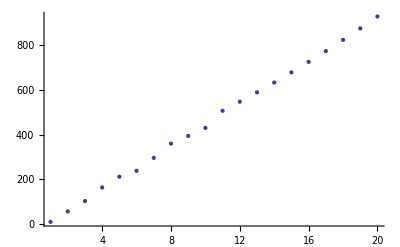

```mathematica
dataplot = ErrorBarPlots`ErrorListPlot[data]
```

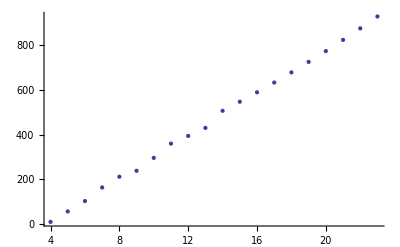

```mathematica
ListPlot[Table[{i+3,data[[i,1]]},{i,1,Length[data]}]]
```

```mathematica
fit=FindFit[Table[data[[i,1]],{i,1,Length[data]}],a x^2+b x+c,{a,b,c},x]
```

{a→-0.0220443,b→48.2671,c→-36.59}

```mathematica
F[x_]:=a x^2+b x+c
```

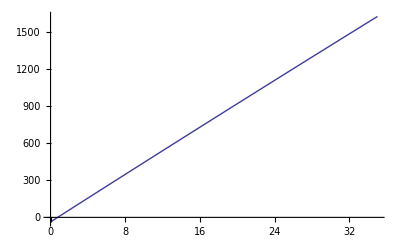

```mathematica
fitplot=Plot[F[x]/.fit,{x,0,35}]
```

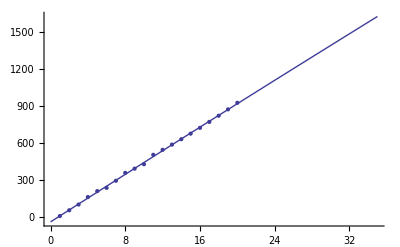

```mathematica
Show[dataplot,fitplot]
```

```mathematica
ranges[[6]]
```

{295.739,296.483}

```mathematica
ranges[[7]]
```

{429.601,430.344}

```mathematica
val=RoughCritical[ranges[[6,2]]]
```

```mathematica
vaf=RoughCritical[ranges[[7,1]]]
```

```mathematica
FindLs[ranges[[6,2]],ranges[[7,1]],val,vaf,1]
```

FindLs[296.483,429.601]

```mathematica
?FindLs
```

Global`FindLs

FindLs[l0_,lf_,val_,vaf_,range_]:=Module[{mid,vam,lnegs,mnegs,hnegs,res},res={};mid=l0+(lf-l0)/2;lnegs=CountNegs[val];vam=RoughCritical[mid];mnegs=CountNegs[vam];hnegs=CountNegs[vaf];If[lf-l0>range,If[lnegs<mnegs||(lnegs==mnegs&&val⟦1⟧<vam⟦1⟧&&mnegs>0),res=Join[res,FindLs[l0,mid,val,vam,range]];Return[res]];If[mnegs<hnegs||(hnegs==mnegs&&vam⟦1⟧<vaf⟦1⟧&&hnegs>0),res=Join[res,FindLs[mid,lf,vam,vaf,range]];Return[res]];,Print[Found one!];Return[{{l0,lf}}];]]